Read data

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]
```

/home/v.korchagova/Документы/BMSTU/build-RKDG2D-Desktop-Debug

```mathematica
coeffs =Import["alphaCoeffs/0.200000","Table"];
mesh=Import["mesh2D","Table"];
```

```mathematica
hx=mesh[[1,3]]
hy=mesh[[2,3]]
MeshCellArea=hx*hy;
MeshCellRcm=mesh[[4;;]];
nCells=Length@MeshCellRcm;
alpha=Table[Partition[coeffs[[i]],3],{i,1,nCells}];
```

0.01

0.01

#### Construct form functions

```mathematica
Phi0[n_,r_]:=1./(√MeshCellArea)
Phi1[n_,r_List]:=√(12./(hy hx^3))(r[[1]]-MeshCellRcm[[n,1]])
Phi2[n_,r_List]:=√(12./(hy^3 hx))(r[[2]]-MeshCellRcm[[n,2]])
Phi[n_,r_List]:={Phi0[n,r],Phi1[n,r],Phi2[n,r]}
```

#### Reconstruct solution

```mathematica
GetSol[alpha_,n_,numSol_,r_List]:=Sum[Phi[n,r][[i]]alpha[[n,numSol,i]],{i,3}];
```

```mathematica
GetSolDensity[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
GetSolGraphics[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Polygon@Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
```

#### Draw solution

```mathematica
Graphics3D@Table[GetSolGraphics[alpha,i,1],{i,1,nCells}]
```

-Graphics3D-

```mathematica
bou=MeshCellRcm[[All,1]]-hx/2;
```

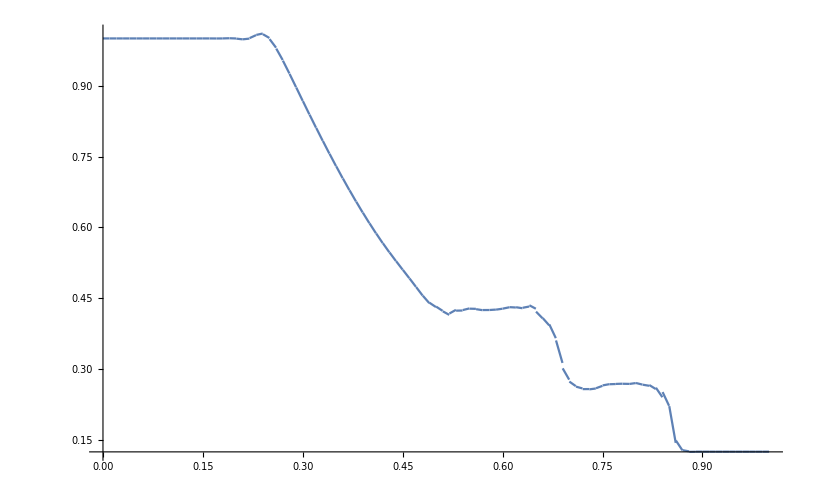

```mathematica
funVis1D[y_]:=Piecewise[Table[{GetSol[alpha,i,1,{0,y}],MeshCellRcm[[i,2]]-hy/2.0 < y <MeshCellRcm[[i,2]]+hy/2.0},{i,1,nCells}]];
funVis1D[x_]:=Piecewise[Table[{GetSol[alpha,i,1,{x,0}],MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,1,nCells}]];
fig=Plot[funVis1D[x],{x,0,1},Exclusions->bou,PlotPoints->100,PlotRange->All]
```

```mathematica
troubledCells={50,51}+1
funVis1DLim[x_]:=Piecewise[Table[{GetSol[alpha,i,1,{x,0}],MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,troubledCells}]];
```

{51,52}

```mathematica
trb=Plot[funVis1DLim[x],{x,0,1},PlotStyle->Red,Exclusions->bou,PlotPoints->200];
```

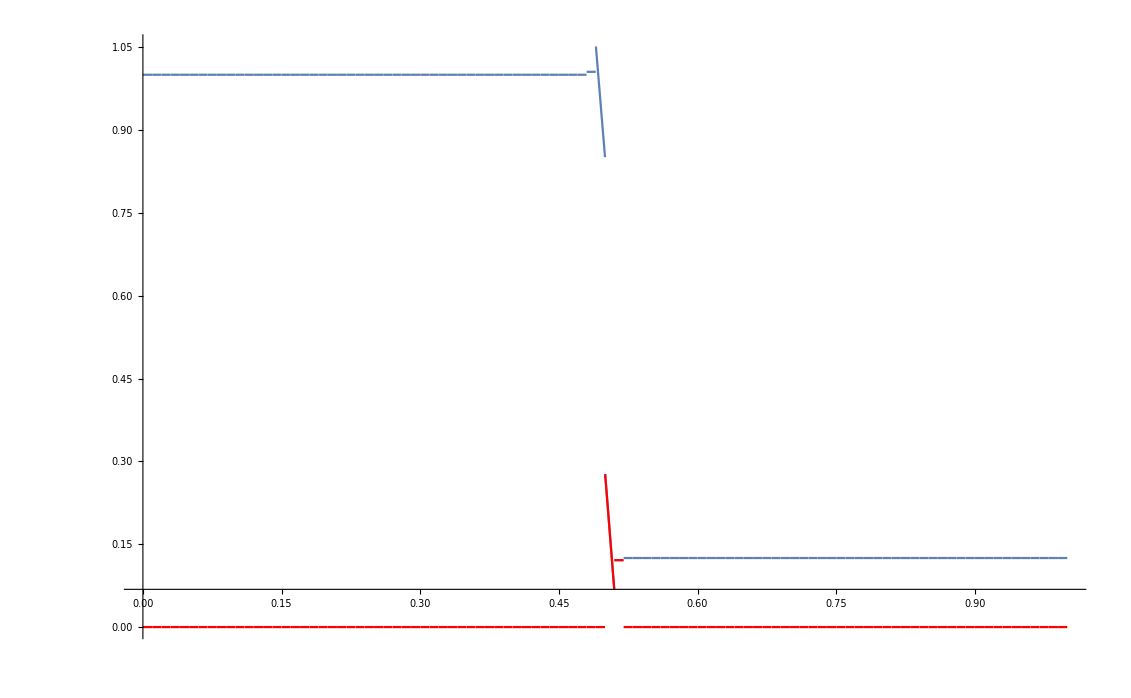

```mathematica
Show[fig,trb]
```

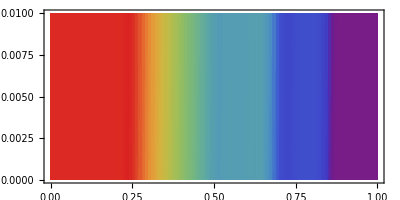

```mathematica
ListDensityPlot[Table[GetSolDensity[alpha,i,1],{i,1,nCells}],AspectRatio->1/2,PlotRange->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```